```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/862nm.dat"]
```

{{1.50189,-0.161273},{1.45414,-0.168644},{1.33983,-0.144067},{1.30748,-0.173425},{1.27821,-0.175855},{1.24682,-0.244967},{1.22351,-0.545538},{1.20659,-0.85402},{1.18213,-1.93213},{1.16419,-inf},{1.15263,-inf},{1.13304,-inf},{1.09662,-0.520724},{1.09807,-0.698059},{1.10207,-0.685735},{1.10747,-0.668884},{1.11401,-0.65722},{1.12685,-0.572754},{1.13867,-0.531675},{1.15401,-0.498502},{1.16573,-0.462321},{1.20258,-0.471477},{1.26466,-0.449542},{1.30748,-0.4689},{1.33983,-0.453343},{1.37936,-0.469332}}

0.196116 (-8.79242+4.87147 -inf)+0.159757 (6.4636-4.30057 -inf) x

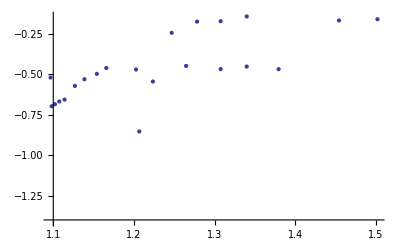

-Graphics-

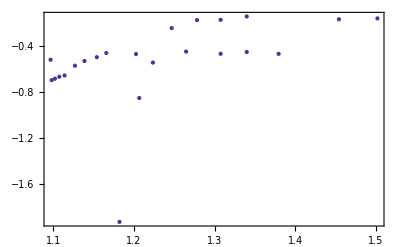

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```